```mathematica
ClearAll["Global`*"];
name=FileNameJoin[{NotebookDirectory[],"./output/multipole_expansion_comparison.dat"}];
ListContourPlot[{#[[1]],#[[2]],Abs[#[[4]]]}&/@Import[name,"Table"],Contours->30]
ListContourPlot[{#[[1]],#[[2]],Abs[#[[5]]]}&/@Import[name,"Table"],Contours->30]
```

Import::nffil: Importの最中にファイル/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_spherical_harmonic/./output/multipole_expansion_comparison.datが見付かりませんでした．

ListContourPlot::arrayerr: $Failedは有効な配列でなければなりません．

ListContourPlot[$Failed,Contours→30]

Import::nffil: Importの最中にファイル/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_spherical_harmonic/./output/multipole_expansion_comparison.datが見付かりませんでした．

ListContourPlot::arrayerr: $Failedは有効な配列でなければなりません．

ListContourPlot[$Failed,Contours→30]

True

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_spherical_harmonic/output/output_n5_A_-10_-10_1_X_10_10_1.txt

True

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_spherical_harmonic/output/output_n6_A_-10_-10_1_X_10_10_1.txt

True

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_spherical_harmonic/output/output_n7_A_-10_-10_1_X_10_10_1.txt

True

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_spherical_harmonic/output/output_n8_A_-10_-10_1_X_10_10_1.txt

True

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_spherical_harmonic/output/output_n9_A_-10_-10_1_X_10_10_1.txt

True

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_spherical_harmonic/output/output_n10_A_-10_-10_1_X_10_10_1.txt

True

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_spherical_harmonic/output/output_n15_A_-10_-10_1_X_10_10_1.txt

True

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_spherical_harmonic/output/output_n20_A_-10_-10_1_X_10_10_1.txt

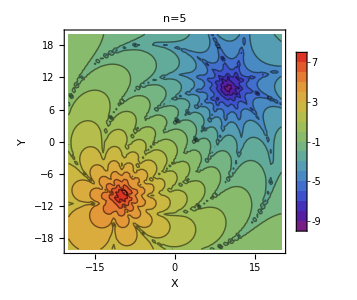
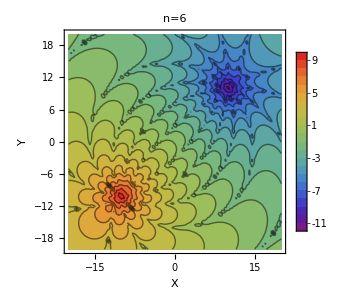
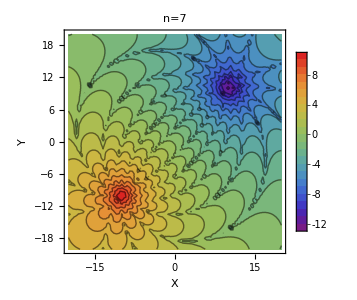
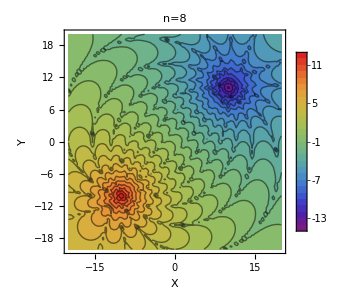
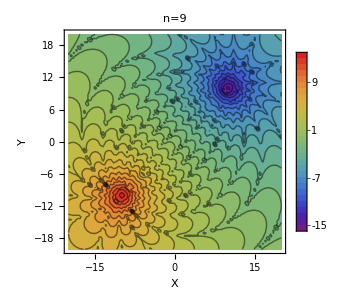
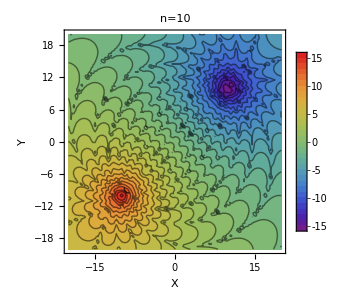
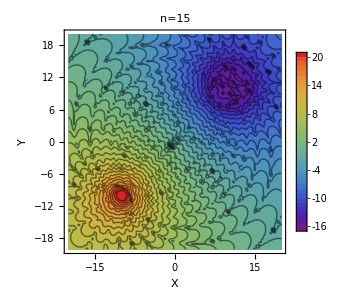
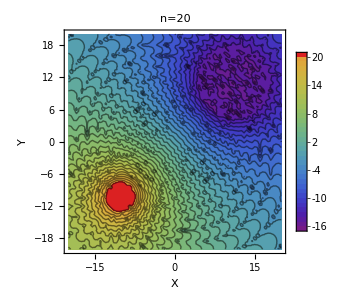

True

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_spherical_harmonic/output/output_n5_A_-10_-10_1_X_10_10_1_switch.txt

True

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_spherical_harmonic/output/output_n6_A_-10_-10_1_X_10_10_1_switch.txt

True

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_spherical_harmonic/output/output_n7_A_-10_-10_1_X_10_10_1_switch.txt

True

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_spherical_harmonic/output/output_n8_A_-10_-10_1_X_10_10_1_switch.txt

True

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_spherical_harmonic/output/output_n9_A_-10_-10_1_X_10_10_1_switch.txt

True

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_spherical_harmonic/output/output_n10_A_-10_-10_1_X_10_10_1_switch.txt

True

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_spherical_harmonic/output/output_n15_A_-10_-10_1_X_10_10_1_switch.txt

True

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_spherical_harmonic/output/output_n20_A_-10_-10_1_X_10_10_1_switch.txt

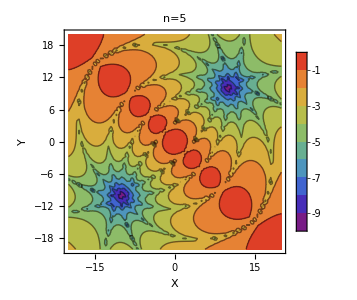
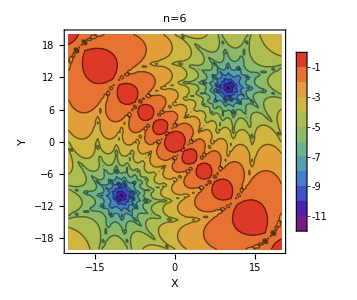
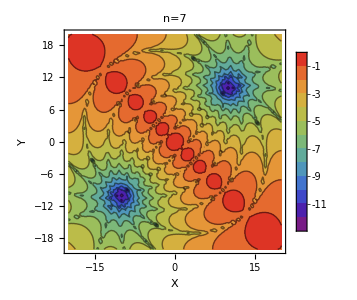
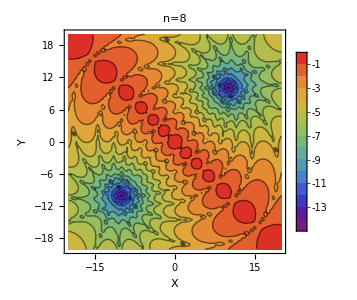
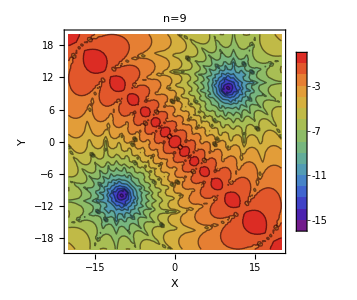
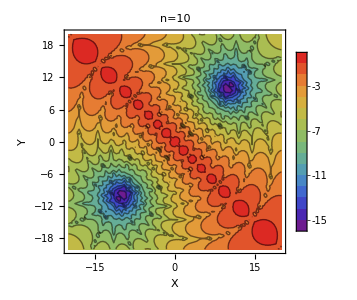
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ClearAll["Global`*"];
Table[
Module[{name,data},
name=ToString@StringForm["output_n``_A_``_``_``_X_``_``_``.txt",n,-10,-10,1,10,10,1];
name=FileNameJoin[{NotebookDirectory[],"output",name}];
data={#[[1]],#[[2]],#[[4]]}&/@Import[name,"Table"];
Print[FileExistsQ[name]];
Print[name];
ListContourPlot[data,
Contours->Table[z,{z,-20,20,1}],
ColorFunction->"Rainbow",
PlotLegends->Automatic,
FrameLabel->{"X","Y"},
InterpolationOrder->1,
ImageSize->300,
PlotLabel->Style[StringForm["n=``",n]]
]
]
,{n,{5,6,7,8,9,10,15,20}}]
Table[
Module[{name,data},
name=ToString@StringForm["output_n``_A_``_``_``_X_``_``_``_switch.txt",n,-10,-10,1,10,10,1];
name=FileNameJoin[{NotebookDirectory[],"output",name}];
data={#[[1]],#[[2]],#[[4]]}&/@Import[name,"Table"];
Print[FileExistsQ[name]];
Print[name];
ListContourPlot[data,
Contours->Table[z,{z,-20,20,1}],
ColorFunction->"Rainbow",
PlotLegends->Automatic,
FrameLabel->{"X","Y"},
InterpolationOrder->1,
ImageSize->300,
PlotLabel->Style[StringForm["n=``",n]]
]
]
,{n,{5,6,7,8,9,10,15,20}}]
```

```mathematica
(*Manipulate[Module[{},
preparedData["output_n"<>ToString[n]<>"_A_"<>ToString[a]<>"_"<>ToString[a]<>"_"<>ToString[a]<>".txt"]]
,{n,4,8,1},{a,-10,10,1}]*)
```